#### define variables

```mathematica
xc = 0;
yc = 0;
npts = 10000;
ri = 1;
kg = 1.1;
minDist=.1;
d=rg-(ri+minDist);
rg = ri *kg;
ptc = {xc,yc};
initialCirclePoints=CirclePoints[ptc,ri,10];
```

#### define functions to use

```mathematica
funcSunnyShady0[x_,y_]:=Sin[.3x]Sin[.5y]
```

```mathematica
funcSunnyShady1[x_,y_]:=Cos[.5x]Sin[.3y]+x
```

```mathematica
funcSunnyShady2[x_,y_]:=x*y
```

```mathematica
funcSunnyShady3[x_,y_]:=2x*y
```

```mathematica
findGradPoints[scalarFunc_,circlePoints_,x_,y_]:=Module[{gradFunc,listGradPoints},
gradFunc=Grad[scalarFunc[x,y],{x,y}];
listGradPoints=gradFunc/.{x->circlePoints[[All,1]],y->circlePoints[[All,2]]};
Transpose[listGradPoints]
]
```

```mathematica
findMaxPoint[listCirclePoints_,listGradPoints_]:=Module[{listNorms,maxPosition,listMaxPoints,listMaxGradPoints,betterListMaxGradPoints},
listNorms=Norm/@listGradPoints;
maxPosition=Position[listNorms,Max[listNorms]];
listMaxGradPoints=listCirclePoints[[#]]&/@maxPosition;
Flatten[RandomChoice[listMaxGradPoints]]
]
```

```mathematica
findNewCenter[oldCenter_,highGradPoint_,d_]:=Module[{v, vhat},
v=highGradPoint-oldCenter;
vhat=v/Norm[v];
vhat d + oldCenter
]
```

```mathematica
doEverything[ptc_,ri_,{scalarFunc_,x_,y_,kg_,minDist_,npts_}]:=Module[{rg,d,initialCirclePoints,listGradPoints,p,ptnew},
rg=ri*kg;
d=rg-(ri+minDist);
initialCirclePoints=CirclePoints[ptc,ri,npts];
listGradPoints=findGradPoints[scalarFunc,initialCirclePoints,x,y];
p=findMaxPoint[initialCirclePoints,listGradPoints];
ptnew=findNewCenter[ptc,p,d];
{ptnew,rg}
]
```

#### find the point on boundary of circle with maximum gradient and the new center point

```mathematica
params={funcSunnyShady3,x,y,kg,minDist,npts};
```

```mathematica
thing0=doEverything[ptc,ri,params];
thing1=doEverything[thing0[[1]],thing0[[2]],params];
thing2=doEverything[thing1[[1]],thing1[[2]],params];
thing3=doEverything[thing2[[1]],thing2[[2]],params];
thing4=doEverything[thing3[[1]],thing3[[2]],params];
thing5=doEverything[thing4[[1]],thing4[[2]],params];
thing6=doEverything[thing5[[1]],thing5[[2]],params];
thing7=doEverything[thing6[[1]],thing6[[2]],params];
thing8=doEverything[thing7[[1]],thing7[[2]],params];
thing9=doEverything[thing8[[1]],thing8[[2]],params];
```

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -√(4 Cos[Times[«2»]]^2+4 Sin[Times[«2»]]^2)+√(4 Cos[(3 π)/10000]^2+4 Sin[(3 π)/10000]^2).

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -√(4 Cos[Times[«2»]]^2+4 Sin[Times[«2»]]^2)+√(4 Cos[π/2000]^2+4 Sin[π/2000]^2).

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -√(4 Cos[Times[«2»]]^2+4 Sin[Times[«2»]]^2)+√(4 Cos[(7 π)/10000]^2+4 Sin[(7 π)/10000]^2).

General::stop: Further output of Max::meprec will be suppressed during this calculation.

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

```mathematica
plt0=Graphics[Circle[thing0[[1]],thing0[[2]]]];
plt1=Graphics[Circle[thing1[[1]],thing1[[2]]]];
plt2=Graphics[Circle[thing2[[1]],thing2[[2]]]];
plt3=Graphics[Circle[thing3[[1]],thing3[[2]]]];
plt4=Graphics[Circle[thing4[[1]],thing4[[2]]]];
plt5=Graphics[Circle[thing5[[1]],thing5[[2]]]];
plt6=Graphics[Circle[thing6[[1]],thing6[[2]]]];
plt7=Graphics[Circle[thing7[[1]],thing7[[2]]]];
plt8=Graphics[Circle[thing8[[1]],thing8[[2]]]];
plt9=Graphics[Circle[thing9[[1]],thing9[[2]]]];
```

```mathematica
p0 = DensityPlot[funcSunnyShady3[x,y],{x,-10,10},{y,-10,10}];
p1=Graphics[Circle[ptc,ri]];
```

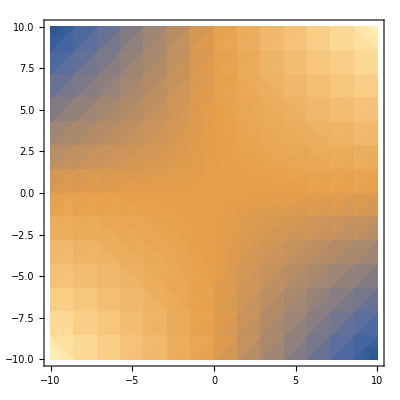

```mathematica
Show[p0]
```



```mathematica
Graphics[Circle[thing1[[1]],thing1[[2]]]]
```

#### draw things

```mathematica
listGraphs={Show[p0],Show[p0,p1],Show[p0,p1,plt0],Show[p0,p1,plt0,plt1],Show[p0,p1,plt0,plt1,plt2],Show[p0,p1,plt0,plt1,plt2,plt3],Show[p0,p1,plt0,plt1,plt2,plt3,plt4],Show[p0,p1,plt0,plt1,plt2,plt3,plt4,plt5],Show[p0,p1,plt0,plt1,plt2,plt3,plt4,plt5,plt6],Show[p0,p1,plt0,plt1,plt2,plt3,plt4,plt5,plt6,plt7],Show[p0,p1,plt0,plt1,plt2,plt3,plt4,plt5,plt6,plt7,plt8],Show[p0,p1,plt0,plt1,plt2,plt3,plt4,plt5,plt6,plt7,plt8,plt9]};
```

```mathematica
ListAnimate[listGraphs]
```

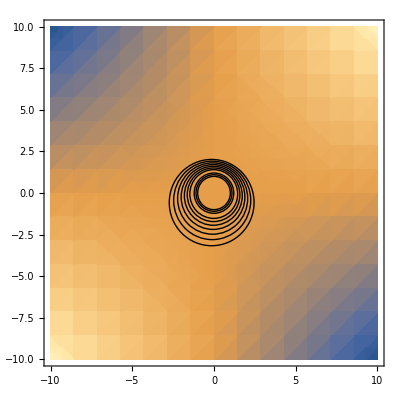

```mathematica
Show[p0,p1,plt0,plt1,plt3,plt4,plt5,plt6,plt7,plt8,plt9,PlotRange->All]
```